# Rappresentazione Grafica delle Funzioni -Graphics- >< Versione Studente ><

## a cura di

Simone Bertolini, Alessio Francesconi, Matteo Grillini

## 1.1 Introduzione

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Equazioni di 1° Grado (Rette)

Teoria

Esercizi

### Equazioni di 2° Grado (Parabole)

Teoria

Esercizi

### Equazioni di 3° Grado

Teoria

Esercizi

Equazioni di 1 °Grado

### Introduzione

Conosciamo la forma delle funzioni di primo grado : f (x) = m X + q ma cosa vogliono dire i parametri m e q?

Ma soprattutto non ti ricorda la forma della retta?

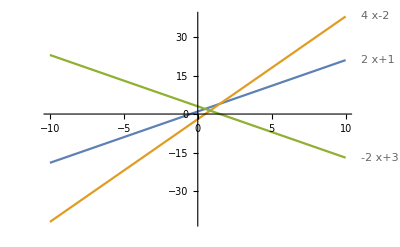

```mathematica
Plot[{2x+1,4x-2,-2x+3}, {x,-10,10},PlotLabels->"Expressions"]
```

### Comprensione guidata del parametro Q

Partiamo cercando di capire cosa rappresenta il q della formula nei grafici :

```mathematica
Manipulate[Plot[2*x+ q ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> 2x+q],{q, -10,+10},{zoom,10,1000}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia q?",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il termine noto q indica l’ordinata del punto di intersezione del grafico con l’asse Y"]}]
```

Hai dubbi su come cambia il grafico quando cambia q?

### Comprensione del caso particolare

```mathematica
p1 = 0
```

0

```mathematica
Hyperlink[{"Student.nb","AG_C1_G1"}]
```

Hai posto attenzione a cosa succede quando q = 0?

Si	No

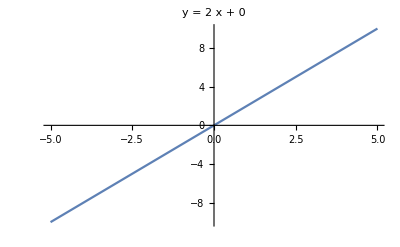

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p1== 0,p1=1;Print[Plot[2x, {x,-5,+5}, PlotLabel->"y = 2 x + 0"]],p1=1]]}]
```

### Analisi guidata del coefficiente di primo grado

Ora abbiamo capito cosa vuol dire il termine noto sul grafico ma il coefficiente di primo grado m come si traduce sul grafico?

```mathematica
Manipulate[Plot[m*x+-2 ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> m x-2],{m, -10,+10},{zoom,10,1000}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia m?” ",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il coefficiente di primo grado indica l’inclinazione del grafico rispetto all’asse X"]}]
```

Hai dubbi su come cambia il grafico quando cambia m?”

### Comprensione del caso particolare

```mathematica
p2=0
```

0

Hai notato cosa cambia se m < 0 o m > 0?

Si	No

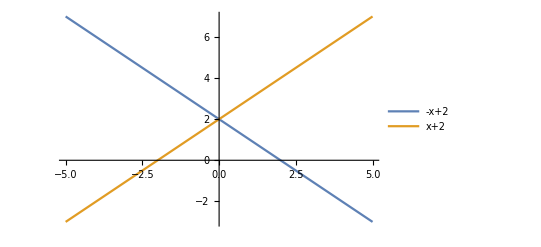

Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p2 == 0,p2=1;Print[Plot[{-x+2,x+2}, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0"],p2=1]]}]
```

### Comprensione del caso particolare

```mathematica
p3=0
```

0

Hai notato cosa succede se m = 0?

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p3 == 0,p3=1;Print[Plot[0x+1, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere il grafico è parallelo all'asse X"],p3=1]]}]
```

Si	No

### Caso particolare X=k

```mathematica
p4=0
```

0

Prima di farti sperimentare liberamente bisogna riflettere su un caso unico delle rette non delle funzioni.
Pensa a quale possa essere e poi scopriamolo insieme.


Il caso delle rette verticali che sono della forma X=k con k che è un qualunque numero.

```mathematica
Manipulate[Plot[x =k,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> 1],{x, -10,+10},{zoom,10,1000}]
```

### Analisi guidata del coefficiente di primo grado

```mathematica
list1={}
```

{}

```mathematica
<||>
a=1
b=1
c=1
q=1
```

<||>

1

1

1

«1 more identical outputs»

```mathematica
DynamicModule[{f},
Column[
{
Panel[
Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x+ q; "", TrackedSymbols:>{a,q}]
Button[
"Add",
If[a== Null || q==Null || a==0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list1,
f
],
AppendTo[
list1,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list1]
```

```mathematica
Dynamic[Plot[list1,{x, -10,10}]]
```

```mathematica
Button[
"Delete",
list1= {}]
```

Delete

Equazioni di 2 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^2+b*x + q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list2 = {}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^2+b*x+ q; "", TrackedSymbols:>{a,b,q}]
Button[
"Add",
If[a== Null ||b== Null || q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list2,
f
],
AppendTo[
list2,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list2]
```

```mathematica
Dynamic[Plot[list2,{x, -10,10}]]
```

```mathematica
Button[
"Delete",
list2= {}]
```

Delete

Equazioni di 3 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^3+b*x ^2+c*x+ q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{c,-10,+10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list3={}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^3 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[c],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^3+b*x^2+c*x + q; "", TrackedSymbols:>{a,b,c,q}]
Button[
"Add",
If[a== Null ||b== Null || c== Null||q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list3,
f
],
AppendTo[
list3,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list3]
```

```mathematica
Dynamic[Plot[list3,{x,-10, 10}]]
```

```mathematica
Button[
"Delete",
list3= {}]
```

Delete

```mathematica
DialogNotebook[Column[{"The changes have been saved.",DefaultButton[]}]]
```

The changes have been saved.

```mathematica
inputSqrt = "x+1"
```

x+1

```mathematica
Button["√x",
CreateDialog[
Column[
{"Insert Value of Sqrt",InputField[
Dynamic[inputSqrt],String,FieldSize->Full
],DefaultButton[]}
]
]
]
```

√x

```mathematica
Dynamic[inputSqrt]
```

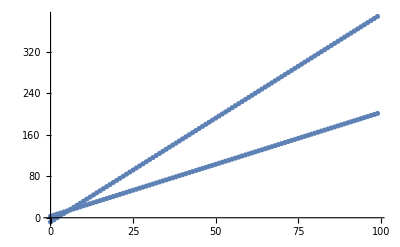

```mathematica
v1={};v2={};
For[t=0,t<100,t=t+1,y=2 t+3;
z=4 t-8;
AppendTo[v1,{t,y}];
AppendTo[v2,{t,z}];]

Show[{ListPlot[v1],ListPlot[v2]},PlotRange->All]
```